```mathematica
(*Sedov parameters*)
Energy = 1.0;
Subscript[ρ, 1] = 1.0;

(*Thermodynamic parameters*)
γ = 1.4;
β = 1.033;

(*Time to start solution at*)
t = 0.02;

(*Shorthands*)
ξ = r/β*(Subscript[ρ, 1]/(Energy*t^2))^(1/5);
u = 0.4*β*(Energy/Subscript[ρ, 1])^0.2*t^0.6;
Subscript[ν, 1] = -(13.0*γ^2 - 7.0*γ + 12.0)/((3.0*γ - 1.0)*(2.0*γ + 1.0));
Subscript[ν, 2] = 5.0* (γ - 1.0)/(2.0*γ + 1.0);
Subscript[ν, 3] = 3.0/(2.0*γ + 1.0);
Subscript[ν, 4] = Subscript[ν, 1]/(2.0-γ);
Subscript[ν, 5] = 2.0/(2.0-γ);

(*Plots used to sample*)
locations = Table[i, {i,0,1, 0.1}];
ξtable = 1/β*(Subscript[ρ, 1]/(Energy*t^2))^(1/5)*locations;

vtable = locations;
gtable = locations;
ztable = locations;

velocitytable = locations;
densitytable = locations;
pressuretable = locations;

For[i = 1, i ≤ Length[locations], i++,
	If[ξtable[[i]] < 1.0,
(*V,G, and Z Tables*)		vtable[[i]] = V/.FindRoot[(ξtable[[i]])^5 - 4.0/((γ + 1)*V^2)*((γ + 1)/(7-γ)*(5-(3*γ-1)*V))^Subscript[ν, 1]*((γ+1)/(γ-1)*(γ*V-1))^Subscript[ν, 2],{V,0.7+locations[[i]]}, AccuracyGoal->3, PrecisionGoal->3, MaxIterations->1000];
					gtable[[i]] = G/.FindRoot[G - (γ+1)/(γ-1)*((γ+1)/(γ-1)*(γ*vtable[[i]] - 1))^Subscript[ν, 3]*((γ+1)/(7-γ)*(5-(3*γ-1)*vtable[[i]]))^Subscript[ν, 4]*((γ+1)/(γ-1)*(1-vtable[[i]]))^Subscript[ν, 5],{G,3.0}, AccuracyGoal->3, PrecisionGoal->3, MaxIterations->1000];
ztable[[i]] = Z/.FindRoot[Z - γ*(γ-1)*((1-vtable[[i]])*(vtable[[i]])^2)/(2*(γ*vtable[[i]]- 1)),{Z,2.0}, AccuracyGoal->3, PrecisionGoal->3, MaxIterations->1000];
(*Actual velocity, density, and pressure*)
		velocitytable[[i]] = 0.4/t*locations[[i]]*vtable[[i]];
		densitytable[[i]] = Subscript[ρ, 1]*gtable[[i]];
		pressuretable[[i]] = 0.16/(γ*t^2)*(locations[[i]])^2*ztable[[i]]*densitytable[[i]],
	(*Else*)
		velocitytable[[i]] = (2.0*u)/(γ + 1);
		densitytable[[i]] = (γ+1)/(γ-1)*Subscript[ρ, 1];
		pressuretable[[i]] = (2.0*u^2)/(γ+1)*Subscript[ρ, 1]
	]
](*End For*);
(*Evaluate: On[FindRoot::lstol]*)
```

```mathematica
velcords = Table[{0,0}, {i,0,1,0.1}];
denscords = velcords;
prescords = velcords;

For[i=1, i≤ Length[locations], i++,
	velcords[[i]] = {locations[[i]], Re[velocitytable[[i]]]};
	denscords[[i]] = {locations[[i]], Re[densitytable[[i]]]};
	prescords[[i]] = {locations[[i]], Re[pressuretable[[i]]]};
](*End For*);

Print[velcords]
Print[denscords]
Print[prescords]
```

{{0.,0.},{0.1,1.4286},{0.2,2.90368},{0.3,0.0329304},{0.4,0.0329304},{0.5,0.0329304},{0.6,0.0329304},{0.7,0.0329304},{0.8,0.0329304},{0.9,0.0329304},{1.,0.0329304}}

{{0.,-0.000135877},{0.1,0.0180018},{0.2,2.98156},{0.3,6.},{0.4,6.},{0.5,6.},{0.6,6.},{0.7,6.},{0.8,6.},{0.9,6.},{1.,6.}}

{{0.,0.},{0.1,92.9994},{0.2,84.6103},{0.3,0.00130129},{0.4,0.00130129},{0.5,0.00130129},{0.6,0.00130129},{0.7,0.00130129},{0.8,0.00130129},{0.9,0.00130129},{1.,0.00130129}}

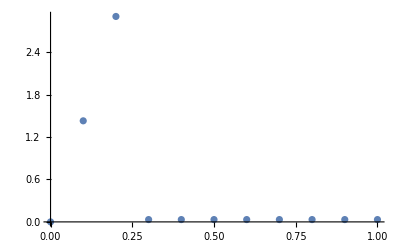

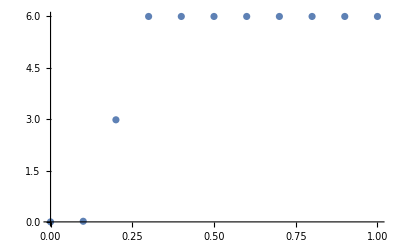

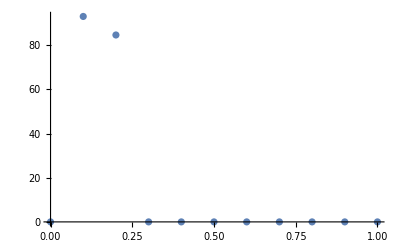

```mathematica
ListPlot[velcords]
ListPlot[denscords]
ListPlot[prescords]
```